```mathematica
f [x_,a_,b_,c_]:= a*(Cos[b*x]+1)/2+c
```

```mathematica
g[x_,a_,b_]:= -a*x^2+b
```

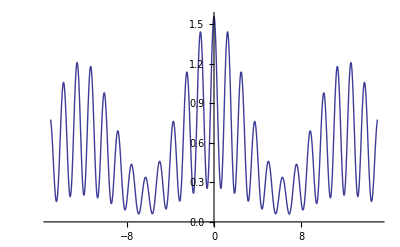

```mathematica
Plot[{f[x,1,5,0.2] *g[x,0.001,1]*f[x,1,0.5,0.3]*g[x,0.0005,1]},{x,-15,15}]
```